```mathematica
Clear["Global`*"]
(*Initialize Parameter*)
Subscript[S, 0]=20;
(*scale factor could be time-dependent*)
u[i_]:= 1+1/(2*i);
d[i_]:= 1-1/i;
r=1/4;
(*n - period*)
n =2; 
(*key in the option function*)
value[ls_]:=Max[ls⟦-1⟧-25,0]; 


(*The following part is the algorithm to compute Subscript[V, 0], user does not need to modify anything*)
i=0;
path = {{}};
map[ls_,i_]:={Append[ls,u[i]],Append[ls,d[i]]};
While[i<n, path = Flatten[(map[#,i+1]& /@path),1];i++];
path;
f[x_,i_]:= If[x⟦i⟧>1,(1+r-d[i])/(u[i]-d[i]),1-(1+r-d[i])/(u[i]-d[i])];
probability[x_]:=Module[{x0=x,probabilitylist = {}},
Do[probabilitylist = AppendTo[probabilitylist, f[x0,i]],{i,Length@x}];
probabilitylist]
probabilitypath = probability/@path;
probabilitypath;
product[ls_]:= Times@@ls;
probabilitypath = product/@ probabilitypath;

g[path_]:=
Module[{factorlist= path,length=Length@path,valuelist={Subscript[S, 0]},i=0},
 Do[valuelist =AppendTo[valuelist, valuelist⟦-1⟧*factorlist⟦i⟧],{i,length}];
valuelist];
valuelist = g/@path;
optionvalue = value/@valuelist;
Subscript[V, 0] = Dot[optionvalue,probabilitypath]/(1+r)^n;
```

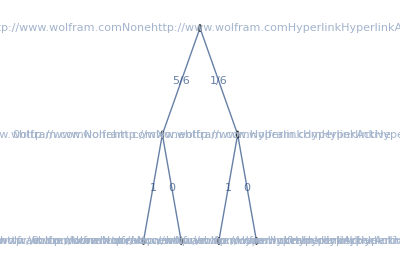

The iniital V_0 is V_0=20/3

The option value at the end is,{25/2,0,0,0}

```mathematica
valpath = {{Subscript[S, 0]}};
hyperlinkLabel[lbl_]:=Hyperlink[lbl,"http://www.wolfram.com",Background->White]
edgelist={};
edgelabel={};
vertexlabel={};
queue={Subscript[S, 0]};
totalnode=2^(n+1)-1;
i=1;
Do[
AppendTo[edgelist,UndirectedEdge[i,2i]];AppendTo[edgelist,UndirectedEdge[i,2i+1]];
t=Floor[Log[2,i]]+1;
cur=queue⟦1⟧;
AppendTo[edgelabel,i<->2i-> (1+r-d[t])/(u[t]-d[t]) ];
AppendTo[edgelabel,i<->2i+1 ->1- (1+r-d[t])/(u[t]-d[t]) ];
AppendTo[vertexlabel,i->Placed[ cur,Center,hyperlinkLabel]];
AppendTo[vertexlabel,2i-> Placed[cur*u[i],Center,hyperlinkLabel]];
AppendTo[vertexlabel,2i+1-> Placed[cur*d[i],Center,hyperlinkLabel]];
AppendTo[queue, cur*u[i]];
AppendTo[queue, cur*d[i]];
queue = Delete[queue,1];
,
{i,1,(totalnode-1)/2}];
TreePlot[Graph[edgelist,EdgeLabels->edgelabel,VertexLabels->vertexlabel]]
Print["The iniital V_0 is V_0=",  Subscript[V, 0]]
Print["The option value at the end is,", optionvalue]
```